# Scattering Kernels in 3D

This is code to accompany the book:
A Hitchhiker’s Guide to Multiple Scattering
© 2022 Eugene d’Eon 
www.eugenedeon.com/hitchhikers

## Cornette-Shanks

[Cornette and Shanks 1992] - Physically reasonable analytic expression for the single-scattering phase function.
Independently proposed [Liu and Weng 2006]

```mathematica
pCornetteShanks[u_,g_]:=3/(8 Pi)((1-g^2)(1+u^2))/((2+g^2)(1+g^2-2 g u)^(3/2))
```

### Normalization condition

```mathematica
Integrate[2 Pi pCornetteShanks[u,g],{u,-1,1},Assumptions->-1<g<1]
```

1

### Mean-cosine

```mathematica
Integrate[2 Pi pCornetteShanks[u,g]u,{u,-1,1},Assumptions->-1<g<1]
```

(3 g (4+g^2))/(5 (2+g^2))

### Legendre expansion coefficients

```mathematica
Integrate[2 Pi (2k+1)pCornetteShanks[Cos[y],g]LegendreP[k,Cos[y]]Sin[y]/.k->0,{y,0,Pi},Assumptions->-1<g<1]
```

1

```mathematica
Integrate[2 Pi (2k+1)pCornetteShanks[Cos[y],g]LegendreP[k,Cos[y]]Sin[y]/.k->1,{y,0,Pi},Assumptions->-1<g<1]
```

(9 g (4+g^2))/(5 (2+g^2))

```mathematica
Integrate[2 Pi (2k+1)pCornetteShanks[Cos[y],g]LegendreP[k,Cos[y]]Sin[y]/.k->2,{y,0,Pi},Assumptions->-1<g<1]
```

(7+80 g^2+18 g^4)/(14+7 g^2)

```mathematica
Integrate[2 Pi (2k+1)pCornetteShanks[Cos[y],g]LegendreP[k,Cos[y]]Sin[y]/.k->3,{y,0,Pi},Assumptions->-1<g<1]
```

(g (27+238 g^2+50 g^4))/(15 (2+g^2))

### sampling

```mathematica
cdf=Integrate[2 Pi pCornetteShanks[u,g],{u,-1,x},Assumptions->-1<g<1&&0<x<1]
```

1/(4 g^3 (2+g^2) √(1+g^2-2 g x))(2-2 g^6-2 g x-2 √(1+g^2-2 g x)+4 g^3 √(1+g^2-2 g x)+g^4 (-5+x^2)+2 g^5 (x+√(1+g^2-2 g x))-g^2 (-5+x^2+4 √(1+g^2-2 g x)))

This CDF can be inverted by solving a quartic equation and simplifying:

```mathematica
sampleCornetteShanksSimplified[xi_,g_]:=Module[{T1,T1a,T2,T3,T4,T5,T6,T7},
T1a=1+2 g^2-2 g^3-g^5+4 g^3 xi+2 g^5 xi;
T1=(T1a)^2;
T2=-4 (-144 g^2+288 g^4-144 g^6)^3;
T4=432 (-1+g^4)^3-1296 (1-g^2) (-1+g^4) (-1-5 g^2+5 g^4+g^6);
T3=(T4+1728 (1-g^2) T1)^2;
T7=(1728 (1-g^2) T1+√(T2+T3)+T4)^(1/3);
T5=(48 2^(1/3) (-g^2+2 g^4-g^6))/((1-g^2) T7);
T6=(2 (-1+g^4))/(1-g^2)+T5+T7/(3 2^(1/3) (1-g^2));
(1+g^2-1/4 (√(6+6 g^2+T6)-√((-6+6 g^4-(16 T1a)/(√(4+(4 g^2 (-4+T5))/T5+T5))+T6-g^2 T6)/(-1+g^2)))^2)/(2 g)
]
```

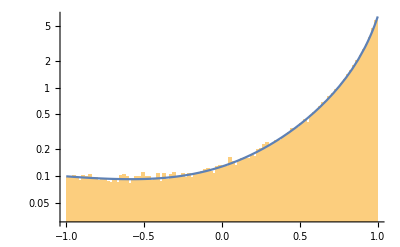

```mathematica
With[{g=.6},
Show[
Histogram[Table[sampleCornetteShanksSimplified[RandomReal[],g],{i,1,100000}],100,"PDF",ScalingFunctions->"Log"],
LogPlot[2 Pi pCornetteShanks[u,g],{u,-1,1},PlotRange->All]
]
]
```